```mathematica
lengths={};
Do[lengths=Append[lengths,Length[tiles2[[i,3]]]],
{i,Length[tiles2]}
];
Count[lengths,2]
(*OR=MapThread[Insert,{OR,ORlengths,Table[4,{Length[ORlengths]}]}];*)
```

```mathematica
Length[Position[tiles2[[All,3]],_?(Length[#]==3&)]]
```

540

```mathematica
ShiftedSpacings//MatrixForm
```

(-4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01
-4.98 | -3.98 | -2.98 | -1.98 | -0.98 | 0.02 | 1.02 | 2.02 | 3.02 | 4.02 | 5.02
-4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01
-5.03 | -4.03 | -3.03 | -2.03 | -1.03 | -0.03 | 0.97 | 1.97 | 2.97 | 3.97 | 4.97
-5.01 | -4.01 | -3.01 | -2.01 | -1.01 | -0.01 | 0.99 | 1.99 | 2.99 | 3.99 | 4.99)

```mathematica
Table[v2[[{1,2}]].i,{i,starvectors[[All,{1,2}]]}]
tmp=testpt.starvectors[[1,{1,2}]]
Table[x-tmp,{x,ShiftedSpacings[[1]]}]
```

{-1.87041,4.02032,5.01096,-1.32872,-5.01096}

-1.86961

{-3.12039,-2.12039,-1.12039,-0.120392,0.879608,1.87961,2.87961,3.87961,4.87961,5.87961,6.87961}

```mathematica
ShiftedSpacings[[3,numlines+1]]
```

5.01

```mathematica
Abs[N[starvectors[[3]]]]
```

{0.587785,0.809017,0.}

```mathematica
Table[Table[Abs[spacing/Abs[starvectors[[i]]].{1,1,0}],{spacing,{ShiftedSpacings[[i,1]],ShiftedSpacings[[i,numlines+1]]}}],{i,Range[numvectors]}]
```

{{4.99,5.01},{3.95215,3.98389},{3.57245,3.58676},{3.60108,3.55813},{3.58676,3.57245}}

```mathematica
Position[ShiftedSpacings[[3]],_?(Chop[#-v2[[{1,2}]].starvectors[[3,{1,2}]]]≥0&)]
```

{}

```mathematica
333333333333333
```

{{10,1},{2,5},{-1.86961,4.83435,0},2}

{-1.86961,4.83435,0}

Part::partw: Part 2 of {{-1.86929, 4.8334}} does not exist.

Part::partw: Part 3 of {{-1.86929, 4.8334}} does not exist.

{5,10,11,5,1}

{5,10,11,5,2}

Dot::dotsh: Tensors {{{-1.86929, 4.8334}} ⟦ 2 ⟧, 0} and {1, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

{}

Dot::dotsh: Tensors {{{-1.86929, 4.8334}} ⟦ 3 ⟧, 0} and {1, 0, 0} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

{}

{-1.86961,4.83435}

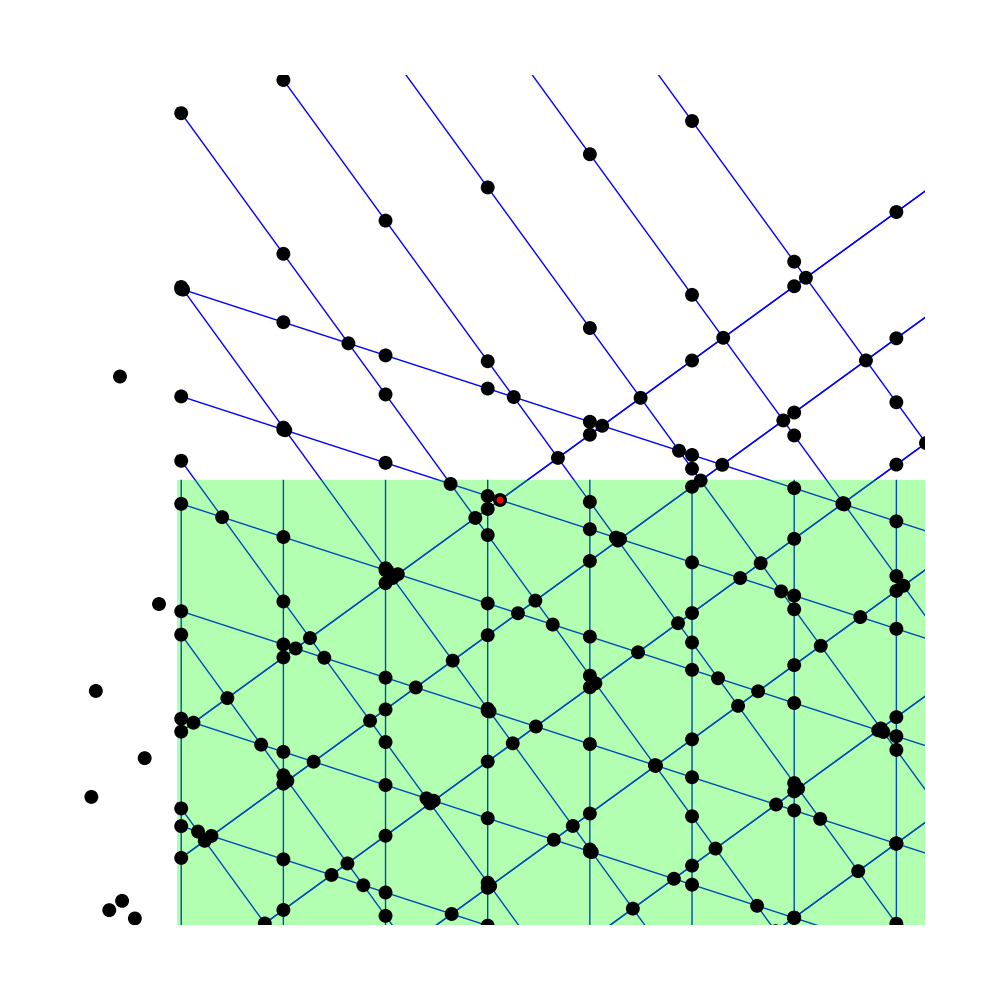

```mathematica
UniqueGridVertices[[633]]
testpt=UniqueGridVertices[[633,3]]

v1=Flatten[{ProbeVectors[[1]],0}];
v2=Flatten[{ProbeVectors[[2]],0}];
v3=Flatten[{ProbeVectors[[3]],0}];

FindGridIndices[testpt]
FindGridIndices[v1]
FindGridIndices[v2]
FindGridIndices[v3]

testpt=testpt[[{1,2}]]
eps=10^-3;
zoom=4;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[testpt+eps*Normalize[n.starvectors][[{1,2}]],{n,ProbeIndices[[{2}]]}]];
ProbeVectorsArrow =Graphics[Line[{testpt,#}]&/@ProbeVectors];

Show[ProbeVectorsArrow,

Table[Plot[-starvectors[[i,1]]/starvectors[[i,2]]*x+ShiftedSpacings[[i,j]]/starvectors[[i,2]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,Range[2,5]},{j,Range[numlines+1]}],
Table[Graphics[{Blue,Thin,Line[{{x,-maxlength},{x,maxlength}}]}],{x,ShiftedSpacings[[1]]}],


Graphics[{Green,Opacity[0.3],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],
Graphics[{PointSize[0.01],Point[UniqueGridVertices[[All,3,{1,2}]]]}](*option here gets rid of indeterminate values*),
Graphics[{PointSize[0.005],Red,Point[testpt]}],
AspectRatio->1,PlotRange->{{testpt[[1]]-zoom,testpt[[1]]+zoom},{testpt[[2]]-zoom,testpt[[2]]+zoom}},
ImageSize->1000
]
```